```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
Clear[partpath,impVoltages,impLatticesites,impCurrents];
partpath="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\PBC hermitian\\current stabilized\\";
(*dir="Input unit cell 4,4,4 1 Vpp after resoldering, 2_43MHz 01";*)
dir="Input unit cell (3,6,6) 0,25 Vpp, 2_285MHz, current stabilized 1.79mArms to less than 0.5% (22.04.05)";

impVoltages=Import[partpath<>dir<>"\\2D_Measurement_01*.dat",HeaderLines->1];
impLatticesites=Import[partpath<>dir<>"\\2D_Measurement_02*.dat",HeaderLines->1];
impCurrents=Import[partpath<>dir<>"\\Current\\2D_Measurement_01*.dat",HeaderLines->1];
(*
impVoltages=Import["G:\\GitHub\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\2D_Measurement_01*.dat",HeaderLines->1];
impLatticesites=Import["G:\\GitHub\\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\2D_Measurement_02*.dat",HeaderLines->1];
impCurrents=Import["G:\\GitHub\\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\Current\\2D_Measurement_01*.dat",HeaderLines->1];
*)
NUnit=8;
NVertical = 8;
```

### Position of current input:

```mathematica
{x,y,z}={7,8,3};
xpos = x;
ypos = y;
zpos = z;
meanVoltages=Map[Mean,Partition[#,100]&/@impVoltages,{2}];
MinMax[Flatten[meanVoltages[[All,All,4]]]];
sortedLatticeSites=(SortBy[#,#[[1]]]&/@impLatticesites);(*Voltage data sorted by increasing Lock-In number -> sort LatticeSites in the same way*)

(*[[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
data=Table[Flatten[{meanVoltages[[m,q,2]]+ⅈ meanVoltages[[m,q,3]],sortedLatticeSites[[m,q,2;;4]],sortedLatticeSites[[m,q,8]]}],{m,1,Dimensions[impVoltages][[1]]},{q,1,4}];
```

```mathematica
(*Split by measurement 1 and 2 -> [[Input 1/2],[Measurements],[Lock-Ins],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
data=Partition[data,(Dimensions[data][[1]])/2];
(*Split into inputs sorted by sublattice sites ->[[SublatticeA/B], [Measurements with all Lock-Ins],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
input1=Partition[SortBy[Flatten[data[[1]],1],#[[5]]&],(Dimensions[data][[2]]*Dimensions[data][[3]])/2];
input2=Partition[SortBy[Flatten[data[[2]],1],#[[5]]&],(Dimensions[data][[2]]*Dimensions[data][[3]])/2];
(*Sort all inputs by unit cells -> 1,1,1, 1,1,2, ... 8,8,7, 8,8,8*)
sortedInput1First=SortBy[input1[[1]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput1Second=SortBy[input1[[2]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput1=Partition[Flatten[{sortedInput1First,sortedInput1Second},1],512];
sortedInput2First=SortBy[input2[[1]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput2Second=SortBy[input2[[2]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput2=Partition[Flatten[{sortedInput2First,sortedInput2Second},1],512];
(*[[Input1/2],[SublatticeSite1/2],[SortedMeasurements],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
sortedInput={sortedInput1,sortedInput2};
shuntresistor=20.;
currentData=(#[[2]]+ⅈ #[[3]])/shuntresistor&/@Flatten[Map[Mean,Partition[#,100]&/@impCurrents,{2}],1];



sortedCurrentInput={{Table[{currentData[[1]]*KroneckerDelta[((NUnit-(z-1)-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,512}],
Table[{0},{512}]},{Table[{0},{512}],Table[{currentData[[2]]*KroneckerDelta[((NUnit-(z-1)-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,512}]}};
```

```mathematica
sortedInput//Dimensions
sortedCurrentInput//Dimensions
```

{2,2,512,5}

{2,2,512,1}

```mathematica
t1 = 1;
t2 = 1;
Position[sortedCurrentInput[[t1,t2,;;,1]],Except[0.+0.I]][[2]]
sortedCurrentInput[[t1,t2,;;]]//MatrixForm
```

{383}

(0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.00176305+0.00011385 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
(* z-index reversed to achieve right handed coordinates *)
```

```mathematica
Vak[i_,kx_,ky_,kz_]:=∑_(k=1)^NUnit (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedInput[[i,1,((NUnit-(k-1)-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit])*Exp[-ⅈ*2*π*kz*k/NUnit];
Vbk[i_,kx_,ky_,kz_]:=∑_(k=1)^NUnit (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedInput[[i,2,((NUnit-(k-1)-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit])*Exp[-ⅈ*2*π*kz*k/NUnit];
Iak[i_,kx_,ky_,kz_]:=∑_(k=1)^NUnit (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedCurrentInput[[i,1,((NUnit-(k-1)-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit])*Exp[-ⅈ*2*π*kz*k/NUnit];
Ibk[i_,kx_,ky_,kz_]:=∑_(k=1)^NUnit (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedCurrentInput[[i,2,((NUnit-(k-1)-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit])*Exp[-ⅈ*2*π*kz*k/NUnit];
kList=Table[(k-1)*(2π/NUnit),{k,1,NUnit}];
kTable = Table[{n,o,p},{n,kList},{o,kList},{p,kList}];


Clear[Lap,Detk];Detk[r_,s_,t_]:= (Vak[1,r,s,t]*Vbk[2,r,s,t])/(Iak[1,r,s,t]*Ibk[2,r,s,t])-(Vbk[1,r,s,t]*Vak[2,r,s,t])/(Iak[1,r,s,t]*Ibk[2,r,s,t]);
Lap[p_,q_,r_]:=LapFkt[p,q,r]=1/Detk[p,q,r]*{{Vbk[2,p,q,r]/Ibk[2,p,q,r],-Vak[2,p,q,r]/Ibk[2,p,q,r]},{-Vbk[1,p,q,r]/Iak[1,p,q,r],Vak[1,p,q,r]/Iak[1,p,q,r]}};
```

```mathematica
Lap[1,1,1]
```

{{0.00335746+0.0017089 ⅈ,0.00394848+0.000638137 ⅈ},{0.00284361+0.00336204 ⅈ,-0.00362346-0.00173411 ⅈ}}

```mathematica
(*
DetLapReal= (sortedInput[[1,1,;;,1]]*sortedInput[[2,2,;;,1]])/(sortedCurrentInput[[1,1,;;,1]]*sortedCurrentInput[[2,2,;;,1]])-(sortedInput[[1,2,;;,1]]*sortedInput[[2,1,;;,1]])/(sortedCurrentInput[[1,1,;;,1]]*sortedCurrentInput[[2,2,;;,1]]);
LapReal=1/DetLapReal*{{sortedInput[[2,2,;;,1]]/sortedCurrentInput[[2,2,;;,1]],-sortedInput[[2,1,;;,1]]/sortedCurrentInput[[2,2,;;,1]]},{-sortedInput[[1,2,;;,1]]/sortedCurrentInput[[1,1,;;,1]],sortedInput[[1,1,;;,1]]/sortedCurrentInput[[1,1,;;,1]]}};
*)
```

```mathematica
Frequency = 2.285*10^6;
Omega = 2*π*Frequency;
LBZ = 27*10^-6;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
Alpha = -Omega/(Omega^2*LBZ);
LBZControl = 1/(Omega*LBZ);
```

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_,kz_}]:=N[(-(CAz+Alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz-Alpha) Cos[ky] X[3]]
```

```mathematica
Clear[n1];
SetSharedVariable[n1];
n1=0;
Monitor[
resultPerMeasComplex=Parallelize[Table[
If[kz==1,n1++];
evals=Eigenvalues[Lap[kx-1,ky-1,kz-1]],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NUnit}]];
(*resultPerCircuitComplex=Parallelize[Table[
If[kz==1,n1++];
evals=Eigenvalues[Lap[kx-1,ky-1,kz-1]],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NUnit}]];*)
,Row[{"Step 1/1 ",ProgressIndicator[n1,{1,NUnit^2}]}]]

resultPerMeas=Table[SortBy[resultPerMeasComplex[[kx,ky,kz]],Im[#]&],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NUnit}];
```

Part::partw: Part 2 of {{{-0.00124473-0.00783055 ⅈ,1.,1.,1.,1.},{-0.0246129-0.05397 ⅈ,2.,1.,1.,1.},{0.000168494+0.000590834 ⅈ,3.,1.,1.,1.},{-0.00437857+0.00368551 ⅈ,4.,1.,1.,1.},{0.001395-0.00691607 ⅈ,5.,1.,1.,1.},«1»,{«1»},{-0.0261287-0.117108 ⅈ,8.,1.,1.,1.},{0.0117672+0.0468358 ⅈ,1.,2.,1.,1.},{-0.00425747-0.00444932 ⅈ,2.,2.,1.,1.},«502»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {{{-0.00124473-0.00783055 ⅈ,1.,1.,1.,1.},{-0.0246129-0.05397 ⅈ,2.,1.,1.,1.},{0.000168494+0.000590834 ⅈ,3.,1.,1.,1.},{-0.00437857+0.00368551 ⅈ,4.,1.,1.,1.},{0.001395-0.00691607 ⅈ,5.,1.,1.,1.},«1»,{«1»},{-0.0261287-0.117108 ⅈ,8.,1.,1.,1.},{0.0117672+0.0468358 ⅈ,1.,2.,1.,1.},{-0.00425747-0.00444932 ⅈ,2.,2.,1.,1.},«502»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
StepXY = 2π/NUnit;
StepZ = 2π/NVertical;
WeylPoint1 = {0,Pi/2,π};
WeylPoint2={0,3 Pi/2,π};
WeylPoint3={π,Pi/2,π};
WeylPoint4 = {π,3Pi/2,π};

shifts2DSide = Flatten@Table[If[Abs[i]+Abs[j]+Abs[k]==3π/4,Nothing,If[Abs[i]+Abs[j]+Abs[k]==0,Nothing,{i,j,k}]],{i,-StepXY,StepXY,StepXY},{j,0,0},{k,-StepZ,StepZ,StepZ}];

shifts2DFront = Flatten@Table[If[Abs[i]+Abs[j]+Abs[k]==3π/4,Nothing,If[Abs[i]+Abs[j]+Abs[k]==0,Nothing,{i,j,k}]],{i,0,0},{j,-StepXY,StepXY,StepXY},{k,-StepZ,StepZ,StepZ}];

shifts = Flatten@Table[If[Abs[i]+Abs[j]+Abs[k]==3π/4,Nothing,If[Abs[i]+Abs[j]+Abs[k]==0,Nothing,{i,j,k}]],{i,-StepXY,StepXY,StepXY},{j,-StepXY,StepXY,StepXY},{k,-StepZ,StepZ,StepZ}];


KVectorsWeyl1 =Table[{WeylPoint1[[1]]+shifts[[1+3i]],WeylPoint1[[2]]+shifts[[2+3i]],WeylPoint1[[3]]+shifts[[3+3i]]},{i,0,(Length@shifts)/3-1,1}];

KVectorsWeyl2 =Table[{WeylPoint2[[1]]+shifts[[1+3i]],WeylPoint2[[2]]+shifts[[2+3i]],WeylPoint2[[3]]+shifts[[3+3i]]},{i,0,(Length@shifts)/3-1,1}];

KVectorsWeyl3 =Table[{WeylPoint3[[1]]+shifts[[1+3i]],WeylPoint3[[2]]+shifts[[2+3i]],WeylPoint3[[3]]+shifts[[3+3i]]},{i,0,(Length@shifts)/3-1,1}];

KVectorsWeyl4 =Table[{WeylPoint4[[1]]+shifts[[1+3i]],WeylPoint4[[2]]+shifts[[2+3i]],WeylPoint4[[3]]+shifts[[3+3i]]},{i,0,(Length@shifts)/3-1,1}];


KVectorsWeyl12DSide =Table[{WeylPoint1[[1]]+shifts2DSide[[1+3i]],WeylPoint1[[2]]+shifts2DSide[[2+3i]],WeylPoint1[[3]]+shifts2DSide[[3+3i]]},{i,0,(Length@shifts2DSide)/3-1,1}];

KVectorsWeyl12DFront =Table[{WeylPoint1[[1]]+shifts2DFront[[1+3i]],WeylPoint1[[2]]+shifts2DFront[[2+3i]],WeylPoint1[[3]]+shifts2DFront[[3+3i]]},{i,0,(Length@shifts2DFront)/3-1,1}];
```

```mathematica
KVectorExperiment[kx_,ky_,kz_]:= KvecExp[kx,ky,kz]= Re@{(Lap[kx,ky,kz][[1,2]]+Lap[kx,ky,kz][[2,1]])/2,I(Lap[kx,ky,kz][[1,2]]-Lap[kx,ky,kz][[2,1]])/2,(Lap[kx,ky,kz][[1,1]]-Lap[kx,ky,kz][[2,2]])/2}

KVectorTheory[kx_,ky_,kz_]:= KvecTheory[kx,ky,kz]= -{(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])),C1 Sin[kz],(CAz-Alpha) Cos[ky]}


KVectorTheory2DSide[kx_,ky_,kz_]:=-{(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])),(CAz-Alpha) Cos[ky]}

KVectorExperiment2DSide[kx_,ky_,kz_]:= Re@{(Lap[kx,ky,kz][[1,2]]+Lap[kx,ky,kz][[2,1]])/2,(Lap[kx,ky,kz][[1,1]]-Lap[kx,ky,kz][[2,2]])/2}


KVectorTheory2DFront[kx_,ky_,kz_]:= -{C1 Sin[kz],(CAz-Alpha) Cos[ky]}

KVectorExperiment2DFront[kx_,ky_,kz_]:= Re@{I(Lap[kx,ky,kz][[1,2]]-Lap[kx,ky,kz][[2,1]])/2,(Lap[kx,ky,kz][[1,1]]-Lap[kx,ky,kz][[2,2]])/2}
```

```mathematica
{Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorExperiment2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]-StepXY,WeylPoint1[[2]],WeylPoint1[[2]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[2]]-1.3StepXY,WeylPoint1[[2]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]],

Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorTheory2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]-StepXY,WeylPoint1[[2]],WeylPoint1[[2]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[2]]-1.3StepXY,WeylPoint1[[2]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]]}
```

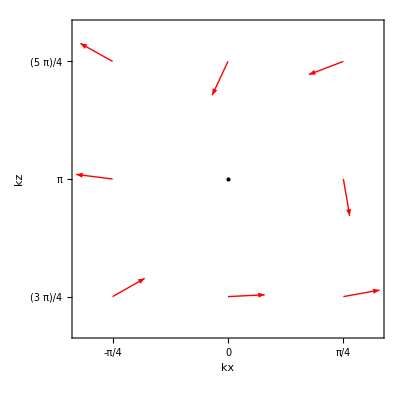
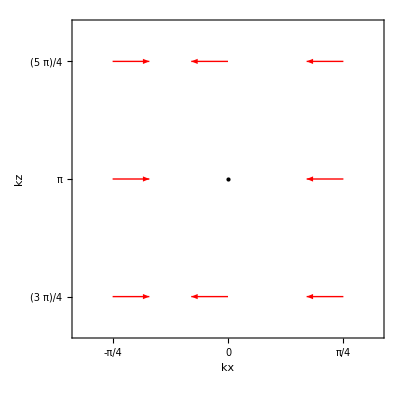

```mathematica
{Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorExperiment2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]-StepXY,WeylPoint1[[1]],WeylPoint1[[1]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[1]]-1.3StepXY,WeylPoint1[[1]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]],

Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorTheory2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]-StepXY,WeylPoint1[[1]],WeylPoint1[[1]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[1]]-1.3StepXY,WeylPoint1[[1]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]]}
```

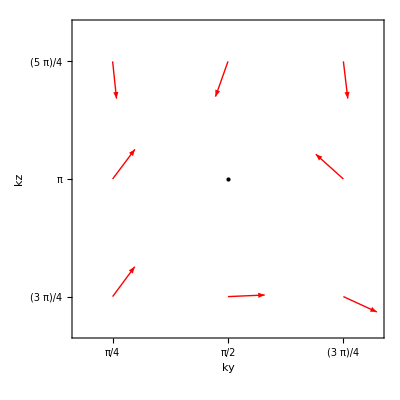

```mathematica
Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorExperiment2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]-StepXY,WeylPoint1[[2]],WeylPoint1[[2]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[2]]-1.3StepXY,WeylPoint1[[2]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]]
```

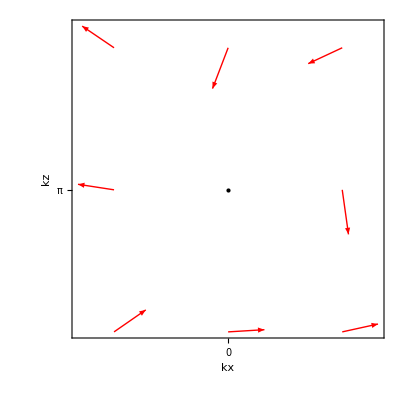

```mathematica
Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorExperiment2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]},{WeylPoint1[[3]]}},ImageSize->400,Frame->True,Axes->False ,AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]]
```

```mathematica
Grid[{{Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorExperiment2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]},{WeylPoint1[[3]]}},ImageSize->400,Frame->True,Axes->False ,AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]],Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorTheory2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]},{WeylPoint1[[3]]}},ImageSize->400,Frame->True,Axes->False ],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]]},{,Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorTheory2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]},{WeylPoint1[[3]]}},ImageSize->400,Frame->True,Axes->False ],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]]}},"Low Energy Vector Field near Weyl Point "<>ToString[WeylPoint1,InputForm]<>"\n"<>"Left: Experiment,  Right: Theory,  Top: kx-kz Plane,  Bottom: ky-kz Plane",Top]
```

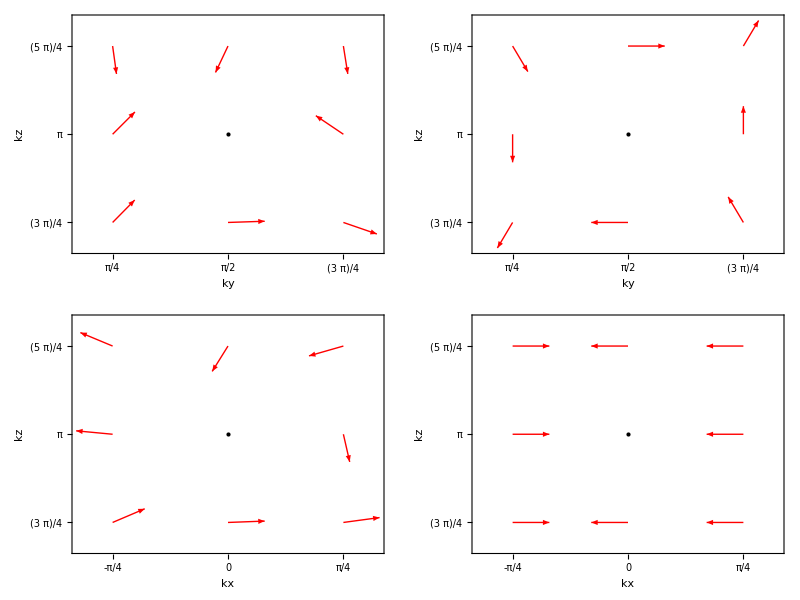
-Graphics-Low Energy Vector Field near Weyl Point {0, Pi/2, Pi}
Left: Experiment,  Right: Theory,  Top: kx-kz Plane,  Bottom: ky-kz Plane

```mathematica
Labeled[Grid[{{Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorExperiment2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]-StepXY,WeylPoint1[[2]],WeylPoint1[[2]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[2]]-1.3StepXY,WeylPoint1[[2]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]],

Show[Graphics[{Red,Arrow[{{#[[2]],#[[3]]},0.25Normalize@KVectorTheory2DFront[#[[1]],#[[2]],#[[3]]]+{#[[2]],#[[3]]}}]}&/@KVectorsWeyl12DFront,FrameLabel->{"ky","kz"},FrameTicks->{{WeylPoint1[[2]]-StepXY,WeylPoint1[[2]],WeylPoint1[[2]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[2]]-1.3StepXY,WeylPoint1[[2]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[2]],WeylPoint1[[3]]}]}]]},

{Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorExperiment2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]-StepXY,WeylPoint1[[1]],WeylPoint1[[1]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[1]]-1.3StepXY,WeylPoint1[[1]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]],

Show[Graphics[{Red,Arrow[{{#[[1]],#[[3]]},0.25Normalize@KVectorTheory2DSide[#[[1]],#[[2]],#[[3]]]+{#[[1]],#[[3]]}}]}&/@KVectorsWeyl12DSide,FrameLabel->{"kx","kz"},FrameTicks->{{WeylPoint1[[1]]-StepXY,WeylPoint1[[1]],WeylPoint1[[1]]+StepXY},{WeylPoint1[[3]]-StepZ,WeylPoint1[[3]],WeylPoint1[[3]]+StepZ}},ImageSize->400,Frame->True,Axes->False ,PlotRange->{{WeylPoint1[[1]]-1.3StepXY,WeylPoint1[[1]]+1.3StepXY},{WeylPoint1[[3]]-1.3StepZ,WeylPoint1[[3]]+1.3StepZ}},AspectRatio->1],Graphics[{PointSize[Large],Black,Point[{WeylPoint1[[1]],WeylPoint1[[3]]}]}]]}},Frame->True,Spacings->{1, 5}],"Low Energy Vector Field near Weyl Point "<>ToString[WeylPoint1,InputForm]<>"\n"<>"Left: Experiment,  Right: Theory,  Top: kx-kz Plane,  Bottom: ky-kz Plane",Top]
```

```mathematica
NUnit=8;
NVertical = 6;
```

```mathematica
δ = 2π/NUnit;
δZ = 2π/NVertical;

kList=Table[(k-1)*(2π/NUnit),{k,1,NUnit}];
kZList=Table[(k-1)*(2π/NVertical),{k,1,NVertical}];

BerryTheory[kx_,ky_,kz_]:=Block[{
es1=Eigensystem[N[Hc[{kx,ky,kz}]]],
es2=Eigensystem[N[Hc[{kx,ky,kz+δZ}]]],
es3=Eigensystem[N[Hc[{kx,ky+δ,kz+δZ}]]],
es4=Eigensystem[N[Hc[{kx,ky+δ,kz}]]]},
ev1=es1[[2,Ordering[es1[[1]]]]];
ev2=es2[[2,Ordering[es2[[1]]]]];
ev3=es3[[2,Ordering[es3[[1]]]]];
ev4=es4[[2,Ordering[es4[[1]]]]];
Table[1/δ^2 1/(2π)Im@Log[(Conjugate[ev1].Transpose[ev2])[[i,i]](Conjugate[ev2].Transpose[ev3])[[i,i]](Conjugate[ev3].Transpose[ev4])[[i,i]](Conjugate[ev4].Transpose[ev1])[[i,i]]],{i,2}]
]

BerryExperiment[kx_,ky_,kz_]:=Block[{
es1=Eigensystem[N[Lap[kx*NUnit/(2π),ky*NUnit/(2π),kz*NVertical/(2π)]]],
es2=Eigensystem[N[Lap[kx*NUnit/(2π),ky*NUnit/(2π),(kz+δZ)*NVertical/(2π)]]],
es3=Eigensystem[N[Lap[kx*NUnit/(2π),(ky+δ)*NUnit/(2π),(kz+δZ)*NVertical/(2π)]]],
es4=Eigensystem[N[Lap[kx*NUnit/(2π),(ky+δ)*NUnit/(2π),kz*NVertical/(2π)]]]},
ev1=es1[[2,Ordering[es1[[1]]]]];
ev2=es2[[2,Ordering[es2[[1]]]]];
ev3=es3[[2,Ordering[es3[[1]]]]];
ev4=es4[[2,Ordering[es4[[1]]]]];
Table[1/δ^2 1/(2π)Im@Log[(Conjugate[ev1].Transpose[ev2])[[i,i]](Conjugate[ev2].Transpose[ev3])[[i,i]](Conjugate[ev3].Transpose[ev4])[[i,i]](Conjugate[ev4].Transpose[ev1])[[i,i]]],{i,2}]
]
```

```mathematica
ChernTheory[kx_]:=δ^2 Sum[BerryTheory[kx,ky,kz],{ky,kList},{kz,kList}]

ChernExperiment[kx_]:= δ^2 Sum[BerryExperiment[kx,ky,kz],{ky,kList},{kz,kZList}]
```

```mathematica
ChernTheoryTable = ParallelTable[Round[ChernTheory[kx],0.01],{kx,kList}];
```

```mathematica
ChernExperimentTable = ParallelTable[Round[ChernExperiment[kz],0.01],{kz,kList}];
```

```mathematica
Labeled[ListPlot[{ChernTheoryTable[[;;,1]],ChernTheoryTable[[;;,2]],ChernExperimentTable[[;;,1]],ChernExperimentTable[[;;,2]]},PlotLabel->"Chern number as function of kx at 2.285 MHz, 8 Boards & stromstabilisiert",PlotStyle->{Red,Red,Green,Blue},PlotLabels->{"Theoretical Data",None,"Measured Data Upper Band","Measured Data Lower Band"},Ticks->{{{1,"0"},{3,"π/2"},{5,"π"},{7,"3π/2"}},Automatic},PlotStyle->PointSize[Medium],ImageSize->Full],{"kx","Chern Number"},{Bottom,Left},RotateLabel->True]
```

-Graphics-kxChern Number

```mathematica
(*---------------------*)
```

```mathematica
Clear[ev1,ev2,normEV1,normEV2]

UTheory[Y_,Z_,{kx_,ky_,kz_}]:= Block[{
es1=Eigensystem[N[Hc[{kx,ky,kz}]]],
es2=Eigensystem[N[Hc[{kx,ky+Y*δ,kz+Z*δZ}]]]},
ev1=es1[[2,Ordering[es1[[1]]]]];
ev2=es2[[2,Ordering[es2[[1]]]]];
normEV1 = Table[Normalize[ev1[[i]]],{i,1,Length@ev1,1}];
normEV2 = Table[Normalize[ev2[[i]]],{i,1,Length@ev2,1}];
Table[(Conjugate[normEV1].Transpose[normEV2])[[i,i]],{i,1,Length@ev2,1}]
]

UExperiment[Y_,Z_,{kx_,ky_,kz_}]:= Block[{
es1=Eigensystem[N[Lap[kx*NUnit/(2π),ky*NUnit/(2π),kz*NVertical/(2π)]]],
es2=Eigensystem[N[Lap[kx*NUnit/(2π),(ky+Y*δ)*NUnit/(2π),(kz+Z*δZ)*NVertical/(2π)]]]},
ev1=es1[[2,Ordering[es1[[1]]]]];
ev2=es2[[2,Ordering[es2[[1]]]]];
normEV1 = Table[Normalize[ev1[[i]]],{i,1,Length@ev1,1}];
normEV2 = Table[Normalize[ev2[[i]]],{i,1,Length@ev2,1}];
Table[(Conjugate[normEV1].Transpose[normEV2])[[i,i]],{i,1,Length@ev2,1}]
]

BerryTheoryV2[kx_,ky_,kz_]:=Block[{
U1Kl=UTheory[1,0,{kx,ky,kz}],
U2Kl1=UTheory[0,1,{kx,ky+δ,kz}],
U1Kl2=UTheory[1,0,{kx,ky,kz+δZ}],
U2Kl=UTheory[0,1,{kx,ky,kz}]
},
Im@Table[Log[(U1Kl[[i]])(U2Kl1[[i]])((U1Kl2[[i]])^-1)((U2Kl[[i]])^-1)],{i,2}]
]

BerryExperimentV2[kx_,ky_,kz_]:=Block[{
U1Kl=UExperiment[1,0,{kx,ky,kz}],
U2Kl1=UExperiment[0,1,{kx,ky+δ,kz}],
U1Kl2=UExperiment[1,0,{kx,ky,kz+δZ}],
U2Kl=UExperiment[0,1,{kx,ky,kz}]
},
Im@Table[Log[(U1Kl[[i]])(U2Kl1[[i]])((U1Kl2[[i]])^-1)((U2Kl[[i]])^-1)],{i,2}]
]

ChernTheoryV2[kx_]:=1/(2π)Sum[BerryTheoryV2[kx,ky,kz],{ky,kList},{kz,kZList}]

ChernExperimentV2[kx_]:=1/(2π)Sum[BerryExperimentV2[kx,ky,kz],{ky,kList},{kz,kZList}]
```

```mathematica
ChernTheoryV2Table= ParallelTable[ChernTheoryV2[kx],{kx,kList}];

ChernExperimentV2Table= ParallelTable[ChernExperimentV2[kx],{kx,kList}];
```

```mathematica
ChernExperimentV2Table
```

{{-4.41744×10^-17,-1.},{-1.06018×10^-16,0.},{1.06018×10^-16,-1.06018×10^-16},{1.06018×10^-16,-1.},{1.,-2.12037×10^-16},{0.,-2.},{7.0679×10^-17,-1.06018×10^-16},{-1.06018×10^-16,5.30092×10^-17}}

```mathematica
Labeled[ListPlot[{ChernTheoryV2Table[[;;,1]],ChernTheoryV2Table[[;;,2]],ChernExperimentV2Table[[;;,1]],ChernExperimentV2Table[[;;,2]]},PlotLabel->"Chern number as function of kx at 2.285 MHz, 8 Boards & stromstabilisiert",PlotStyle->{Red,Red,Green,Blue},PlotLabels->{"Theoretical Data",None,"Measured Data Upper Band","Measured Data Lower Band"},Ticks->{{{1,"0"},{3,"π/2"},{5,"π"},{7,"3π/2"}},Automatic},PlotStyle->PointSize[Medium],ImageSize->Full],{"kx","Chern Number"},{Bottom,Left},RotateLabel->True]
```

-Graphics-kxChern Number

```mathematica
newResultPerTotMeas1=Flatten[Table[{kList[[i]],kList[[j]],kZList[[l]],Im[resultPerMeas[[If[i==NUnit,1,i],If[j==NUnit,1,j],If[l==NVertical,1,l],1]]]},{i,1,NUnit},{j,1,NUnit},{l,1,NVertical}],2];
newResultPerTotMeas2=Flatten[Table[{kList[[i]],kList[[j]],kZList[[l]],Im[resultPerMeas[[If[i==NUnit,1,i],If[j==NUnit,1,j],If[l==NVertical,1,l],2]]]},{i,1,NUnit},{j,1,NUnit},{l,1,NVertical}],2];
newResultPerTotMeas={newResultPerTotMeas1,newResultPerTotMeas2};
```

```mathematica
Nvertical = 8;
NVertical = Nvertical;

xcords=Join[Subdivide[0,Pi,4],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1]];

ycords=Join[Subdivide[0,0,4],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[0,0,4-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1]];

zcords=Join[Subdivide[0,0,4*4],Subdivide[2Pi/NVertical,Pi,NVertical/2-1],Subdivide[Pi,Pi,4*4-1]];

path=Table[{xcords[[i]],ycords[[i]],zcords[[i]]},{i,1,Length[xcords]}];

pathTheoretical=Table[{xcords[[i]],ycords[[i]],zcords[[i]]},{i,1,Length[xcords]}];
```

```mathematica
LowerBandPathVals = Table[newResultPerTotMeas[[1,Position[newResultPerTotMeas[[1,;;,1;;3]],path[[i]]][[1,1]],4]],{i,1,Length[path]}];
UpperBandPathVals = Table[newResultPerTotMeas[[2,Position[newResultPerTotMeas[[2,;;,1;;3]],path[[i]]][[1,1]],4]],{i,1,Length[path]}];

LowerBandPathValsTheory = Table[Det[Hc[path[[i]]]],{i,1,Length[path]}];
UpperBandPathValsTheory = Table[-Det[Hc[path[[i]]]],{i,1,Length[path]}];
```

```mathematica
evals=Table[SortBy[Eigenvalues[Lap[path[[i,1]]*NUnit/(2π),path[[i,2]]*NUnit/(2π),path[[i,3]]*NVertical/(2π)]],Im[#]&],{i,1,Length[path]}];
```

```mathematica
Labeled[ListLinePlot[{Im@evals[[;;,1]],Im@evals[[;;,2]],LowerBandPathValsTheory*120.5,UpperBandPathValsTheory*120.5},ImageSize->Large,Mesh->All,PlotLabel->"PBC Spectrum at 2.285 MHz, 8 Boards & stromstabilisiert",PlotStyle->{Blue,Blue,Black,Black},PlotRange->{{-1,40},All},PlotLabels->{"Measured Data",None,"Theoretical Data",None},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{21,"Z"},{25,"U"},{29,"R"},{33,"T"},{37,"Z"}}, Automatic}],{"","j_n"},{Bottom,Left},RotateLabel->True]
```

-Graphics-j_n

```mathematica
(*---------------------*)
```

```mathematica
Labeled[ListLinePlot[{UpperBandPathVals,LowerBandPathVals,LowerBandPathValsTheory*120.53050993346844,UpperBandPathValsTheory*120.53050993346844},Mesh->All,PlotLabel->"PBC Spectrum",PlotStyle->{Blue,Blue,Black,Black},PlotRange->{{-1,40},All},PlotLabels->{"Measured Data",None,"Theoretical Data",None},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{21,"Z"},{25,"U"},{29,"R"},{33,"T"},{37,"Z"}}, Automatic}],{"","j_n"},{Bottom,Left},RotateLabel->True]
```

-Graphics-j_n

```mathematica
{{-Graphics-}, {□}}"""\!\(\*SubscriptBox[\(j\), \(n\)]\)"
```

{{-Graphics-},{□}}j_n

{{-Graphics-},{□}}j_n